```mathematica
SetsToSymbol2[s_]:=Symbol["v"<>StringRiffle[Map[StringJoin[Map[IntegerString[#,36]&,#]]&,s],"x"]]
```

```mathematica
SetsToSymbol2[{{19},{20}}]
```

vjxk

```mathematica
IntegerString[20,32]
```

k

```mathematica
FindFullFormula[g_,v_]:=Block[{edge,pos1,pos2,v2},
If[CompleteGraphQ[g],
{SetsToSymbol2[v]},
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
Join[
FindFullFormula[EdgeAdd[g,edge],v],
FindFullFormula[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
]
]
```

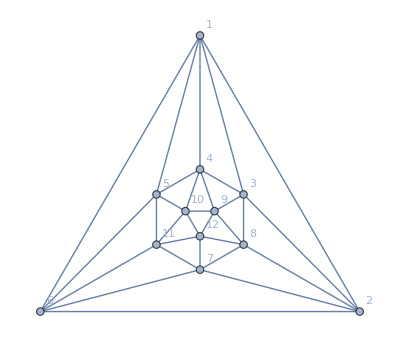

```mathematica
gz=Graph[plantri[[1]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
summa=Total[FindFullFormula[gz,Table[{k},{k,VertexCount[gz]}]]]
```

v17x24x35x68x9bxaxc+v17x24x35x68x9xaxbxc+v17x24x35x69x8axbxc+v17x24x35x69x8bxaxc+v17x24x35x69x8xaxbxc+v17x24x35x6ax8bx9xc+v17x24x35x6ax8x9bxc+v17x24x35x6ax8x9xbxc+v17x24x35x6cx8ax9b+v17x24x35x6cx8ax9xb+v17x24x35x6cx8bx9xa+v17x24x35x6cx8x9bxa+v17x24x35x6cx8x9xaxb+v17x24x35x6x8ax9bxc+v17x24x35x6x8ax9xbxc+v17x24x35x6x8bx9xaxc+v17x24x35x6x8x9bxaxc+26759+v6x735x9xa18xbxc24+v6x735x9xaxb18xc24+v6x79xa18xb24xc35+v6x7x9xa18xb24xc35+v6x8ax917xb24xc35+v6x8x917xaxb24xc35+v6x8x9xa17xb24xc35+v735xa18xb29xc46+v735xa68xb19xc24+v846xa17xb29xc35+v846xa37xb19xc25+v917xa36xb48xc25+v917xa68xb24xc35+v925xa17xb48xc36+v925xa37xb18xc46+v957xa18xb24xc36+v957xa36xb18xc24
 |  |  |  |

```mathematica
summa2=Total[FindFullFormula[EdgeDelete[CompleteGraph[10],9->10],Table[{k},{k,10}]]]
```

v1x2x3x4x5x6x7x8x9a+v1x2x3x4x5x6x7x8x9xa

```mathematica
FormulaGraph2[formula_]:=Block[{sets=Sort[Map[SymbolToSets[#]&,ListofVars[formula]]], edges={},vertices,pos=1},
Monitor[
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol2[s2]->SetsToSymbol2[s1]]]
,{s2,Select[sets,#≠s1&]}
];pos++
,{s1,sets}],
{Length[edges],pos, Length[sets],s1,s2}
];
vertices = Table[SetsToSymbol[s]-> SymbolToLabel[ SetsToSymbol2[s]],{s,sets}];
Graph[edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding", ImageSize->{200,200}]
]
```

```mathematica
SymbolToSets[v1x2x3x4x5x6x7x8x9xaxbxc]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12}}

```mathematica
(*FormulaGraph2[summa2]*)
```

```mathematica
(*FormulaGraph2[summa]*)
```

```mathematica
SymbolToSets2[s_]:=Sort[Map[Sort,SymbolToSets[s]]]
```

```mathematica
SplitFormula[exp_]:=Block[{vars=ListofVars[exp],result=Association[],s,l},
Table[result[k]={},{k,1,12}];
Monitor[
Table[
s=SymbolToSets2[v];
l=Length[s];
result[l]=Append[result[l],s]
,{v,vars}
],
v];
result
]
```

```mathematica
split=SplitFormula[summa]
```

<|1→{},2→{},9,12→{{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12}}}|>
 |  |  |  |

```mathematica
Table[Length[split[k]],{k,1,12}]
```

{0,0,0,10,660,4908,10008,7900,2800,470,36,1}

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[gz,x]]
```

{0,0,0,0,10,660,4908,10008,7900,2800,470,36,1}

```mathematica
TableForm[split[4]//Sort,TableDepth->1]
```

{{1,7,9},{2,4,11},{3,5,12},{6,8,10}}
{{1,7,9},{2,5,12},{3,6,10},{4,8,11}}
{{1,7,10},{2,5,9},{3,6,12},{4,8,11}}
{{1,7,10},{2,9,11},{3,5,12},{4,6,8}}
{{1,8,10},{2,4,11},{3,6,12},{5,7,9}}
{{1,8,10},{2,9,11},{3,5,7},{4,6,12}}
{{1,8,11},{2,4,12},{3,6,10},{5,7,9}}
{{1,8,11},{2,5,9},{3,7,10},{4,6,12}}
{{1,9,11},{2,4,12},{3,5,7},{6,8,10}}
{{1,9,11},{2,5,12},{3,7,10},{4,6,8}}

```mathematica
TableForm[Take[split[5],20]//Sort,TableDepth->1]
```

{{1,7},{2,4},{9,11},{3,5,12},{6,8,10}}
{{1,7},{2,9},{4,11},{3,5,12},{6,8,10}}
{{1,7},{2,9},{5,12},{3,6,10},{4,8,11}}
{{1,7},{2,9},{6,10},{3,5,12},{4,8,11}}
{{1,7},{2,10},{5,9},{3,6,12},{4,8,11}}
{{1,7},{2,10},{6,9},{3,5,12},{4,8,11}}
{{1,7},{2,10},{9,11},{3,5,12},{4,6,8}}
{{1,7},{2,12},{5,9},{3,6,10},{4,8,11}}
{{1,7},{3,5},{4,12},{2,9,11},{6,8,10}}
{{1,7},{3,5},{8,10},{2,9,11},{4,6,12}}
{{1,7},{3,5},{9,11},{2,4,12},{6,8,10}}
{{1,7},{3,10},{5,8},{2,9,11},{4,6,12}}
{{1,7},{3,10},{5,12},{2,9,11},{4,6,8}}
{{1,7},{3,10},{6,9},{2,5,12},{4,8,11}}
{{1,7},{3,10},{6,12},{2,5,9},{4,8,11}}
{{1,7},{3,10},{8,11},{2,5,9},{4,6,12}}
{{1,7},{3,10},{9,11},{2,5,12},{4,6,8}}
{{1,7},{3,11},{4,12},{2,5,9},{6,8,10}}
{{1,7},{3,11},{5,9},{2,4,12},{6,8,10}}
{{1,7},{3,11},{8,10},{2,5,9},{4,6,12}}

```mathematica
IsRefinement[{{1,2}},{{1},{2}}]
```

True

```mathematica
EliminateObvious[assoc_]:=Block[{i,tops,botts, newtops,newAssoc=Association[], found,pos1,pos2},

Monitor[
For[i=12,i≥4,i--,
tops=assoc[i];
botts=assoc[i-1];
newtops={};
pos1=1;
Table[
found=False;
pos2=1;
Table[
If[IsRefinement[bottom,top],found=True;
Goto[done]
];
pos2++
,{bottom,botts}
];
Label[done];
pos1++;
If[!found,
newtops=Append[newtops,top]
]
,{top,tops}
];
newAssoc[i]=newtops;
],
{i,pos1,Length[tops],pos2,Length[botts]}
];
newAssoc
]
```

```mathematica
splat=EliminateObvious[split]
```

<|12→{},11→{},10→{},9→{},8→{},7→{},6→{1},5→{{{1,7},{2,4},{9,11},{3,5,12},{6,8,10}},{{1,7},{2,9},{4,11},{3,5,12},{6,8,10}},{{1,7},{2,9},{5,12},{3,6,10},{4,8,11}},535,{{6},{9,11},{1,8,10},{2,4,12},{3,5,7}},{{6},{7,9},{1,8,10},{2,4,11},{3,5,12}}},4→{{{1,8,10},{2,9,11},{3,5,7},{4,6,12}},{{1,9,11},{2,4,12},{3,5,7},{6,8,10}},{{1,7,10},{2,9,11},{3,5,12},{4,6,8}},{{1,9,11},{2,5,12},{3,7,10},{4,6,8}},{{1,7,9},{2,5,12},{3,6,10},{4,8,11}},{{1,7,9},{2,4,11},{3,5,12},{6,8,10}},{{1,7,10},{2,5,9},{3,6,12},{4,8,11}},{{1,8,11},{2,5,9},{3,7,10},{4,6,12}},{{1,8,10},{2,4,11},{3,6,12},{5,7,9}},{{1,8,11},{2,4,12},{3,6,10},{5,7,9}}}|>
 |  |  |  |

```mathematica
Length[splat[6]]
```

908

```mathematica
Length[splat[5]]
```

540

```mathematica
Length[splat[4]]
```

10

```mathematica
Length[split[11]]
```

36

```mathematica
IsRefinement[{{1,2}},{{1},{2}}]
```

```mathematica
splat[12]//Length
```

1

```mathematica
split[5]
```

{{{1,7},{2,4},{9,11},{10,6,8},{12,3,5}},{{1,7},{2,9},{4,11},{10,6,8},{12,3,5}},{{1,7},{2,9},{5,12},{10,3,6},{11,4,8}},{{1,7},{2,9},{6,10},{11,4,8},{12,3,5}},{{1,7},{2,10},{5,9},{11,4,8},{12,3,6}},{{1,7},{2,10},{6,9},{11,4,8},{12,3,5}},{{1,7},{2,10},{8,4,6},{9,11},{12,3,5}},{{1,7},{2,12},{5,9},{10,3,6},{11,4,8}},644,{{6,10},{7,3,5},{8},{11,1,9},{12,2,4}},{{6,10},{7,3,5},{9},{11,1,8},{12,2,4}},{{6,10},{8},{9,1,7},{11,2,4},{12,3,5}},{{6,12},{7,3,5},{9},{10,1,8},{11,2,4}},{{6},{7,3,5},{8,10},{11,1,9},{12,2,4}},{{6},{7,3,5},{9,11},{10,1,8},{12,2,4}},{{6},{7,9},{10,1,8},{11,2,4},{12,3,5}},{{6},{8,10},{9,1,7},{11,2,4},{12,3,5}}}
 |  |  |  |

```mathematica
split[6]//Tally
```

{{{2,2,2,2,2,2},368},{{1,2,2,2,2,3},2520},{{1,1,2,2,3,3},1920},{{1,1,1,3,3,3},100}}

```mathematica
split[7]//Tally
```

{{{1,1,2,2,2,2,2},3648},{{1,1,1,2,2,2,3},5400},{{1,1,1,1,2,3,3},960}}

```mathematica
split[8]//Tally
```

{{{1,1,1,1,2,2,2,2},5160},{{1,1,1,1,1,2,2,3},2640},{{1,1,1,1,1,1,3,3},100}}

```mathematica
split[9]//Tally
```

{{{1,1,1,1,1,1,2,2,2},2380},{{1,1,1,1,1,1,1,2,3},420}}

```mathematica
split[10]//Tally
```

{{{1,1,1,1,1,1,1,1,2,2},450},{{1,1,1,1,1,1,1,1,1,3},20}}

```mathematica
split[11]//Tally
```

{{{1,1,1,1,1,1,1,1,1,1,2},36}}

```mathematica
split[12]//Tally
```

{{{1,1,1,1,1,1,1,1,1,1,1,1},1}}

```mathematica
split[11]
```

{{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2},{1,1,1,1,1,1,1,1,1,1,2}}